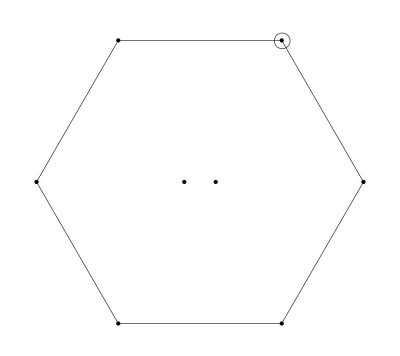

Y=1.5,  I_3=0.5

-2uu(ūs̄+s̄ū)-(ud+du)(s̄d̄+d̄s̄)-2(us+su)s̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

-((d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T))-(d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_b 1C((s̄)_a)^T)-(d_a^T C1 u_b+u_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)-(d_a^T C1 u_b+u_a^T C1 d_b) ((s̄)_b 1C((d̄)_a)^T)-2 ((s̄)_a 1C((s̄)_b)^T) (s_a^T C1 u_b+u_a^T C1 s_b)-2 ((s̄)_b 1C((s̄)_a)^T) (s_a^T C1 u_b+u_a^T C1 s_b)-2 (u_a^T C1 u_b) ((s̄)_a 1C((ū)_b)^T+(s̄)_b 1C((ū)_a)^T)-2 (u_a^T C1 u_b) ((ū)_a 1C((s̄)_b)^T+(ū)_b 1C((s̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 u-d̄(γ^μ).(γ̄)^5 u s̄(γ^μ).(γ̄)^5 d-d̄ γ^μ d s̄ γ^μ u-d̄ γ^μ u s̄ γ^μ d+(d̄(γ̄)^5 d+2 (s̄(γ̄)^5 s)) (s̄(γ̄)^5 u)+d̄(γ̄)^5 u s̄(γ̄)^5 d-1/2 (d̄ σ^μν d s̄ σ^μν u)-1/2 (d̄ σ^μν u s̄ σ^μν d)+(d̄ 1d+2 (s̄ 1s)) (s̄ 1u)+d̄ 1u s̄ 1d-2 (s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 u)-2 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)-2 (s̄ γ^μ s s̄ γ^μ u)-2 (s̄ γ^μ u ū γ^μ u)+2 (s̄(γ̄)^5 u ū(γ̄)^5 u)-s̄ σ^μν s s̄ σ^μν u-s̄ σ^μν u ū σ^μν u+2 (s̄ 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(384 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(96 π^5)-(⟨ d̄ d⟩ log(-q^2/μ^2) (m_d+m_s+m_u) q^4)/(6 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (2 m_d+17 m_s+8 m_u) q^4)/(12 π^4)-(⟨ ū u⟩ log(-q^2/μ^2) (2 m_d+8 m_s+17 m_u) q^4)/(12 π^4)-(2 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(864 π^6)-(4 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(4 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(23 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(72 π^2)+(5 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)+(5 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)+(5 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(36 π^2)-(13 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(18 π^2)-(13 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(18 π^2)+(5 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)-(13 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(18 π^2)-(13 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(18 π^2)-(2 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(10 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(10 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-⟨ d̄ Gd⟩^2/(96 π^2 q^2)+(127 ⟨ s̄ Gs⟩^2)/(288 π^2 q^2)+(127 ⟨ ū Gu⟩^2)/(288 π^2 q^2)-(⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)-(⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)-(20 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(115 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(576 π^2 q^2)+(115 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(576 π^2 q^2)+(127 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(144 π^2 q^2)-(8 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (16 m_s-16 m_u))/(9 q^2)-(2 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (-8 m_d+4 m_s-8 m_u))/(9 q^2)-(32 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/(9 q^2)-(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (m_s+2 m_u))/(9 q^2)-(2 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (-8 m_d-8 m_s+4 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (16 m_u-16 m_s))/(9 q^2)-(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (10 (m_s+m_u)-8 m_d))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

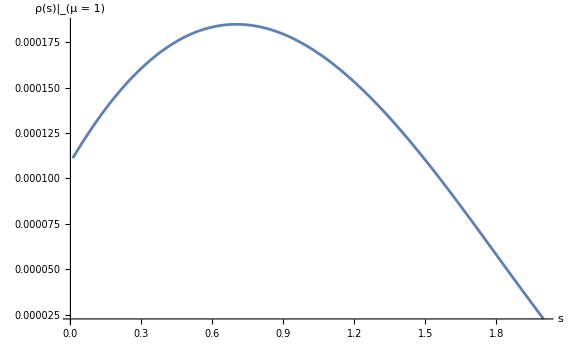
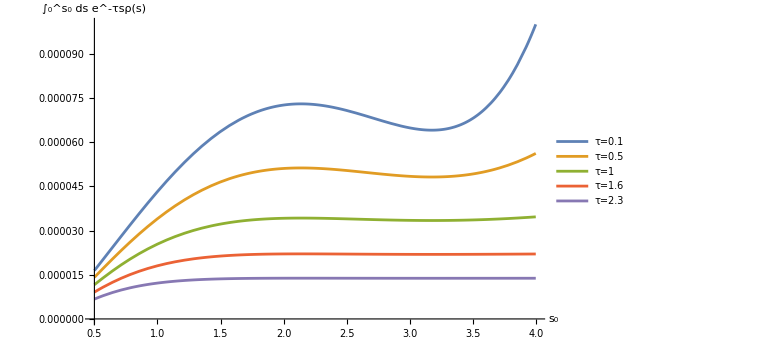

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

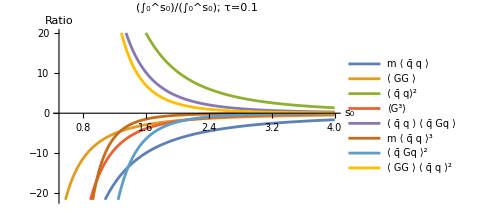
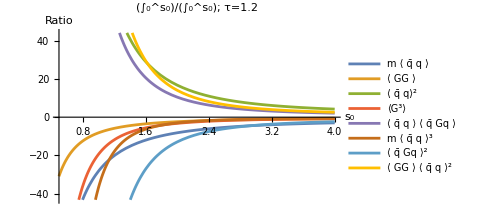
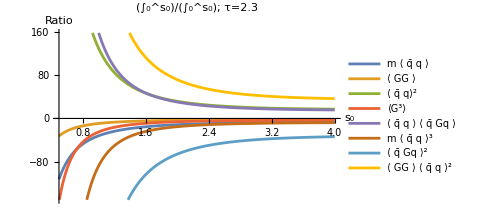

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

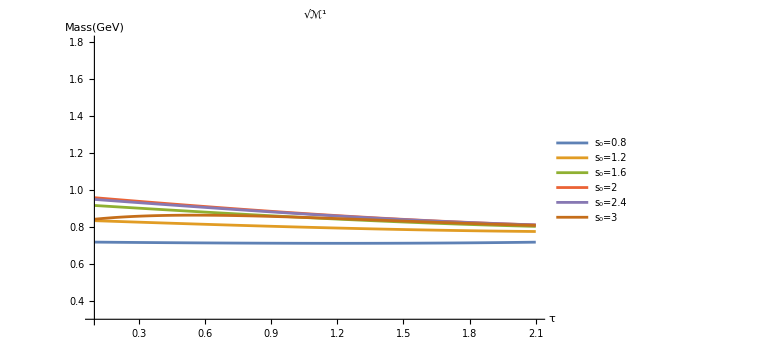
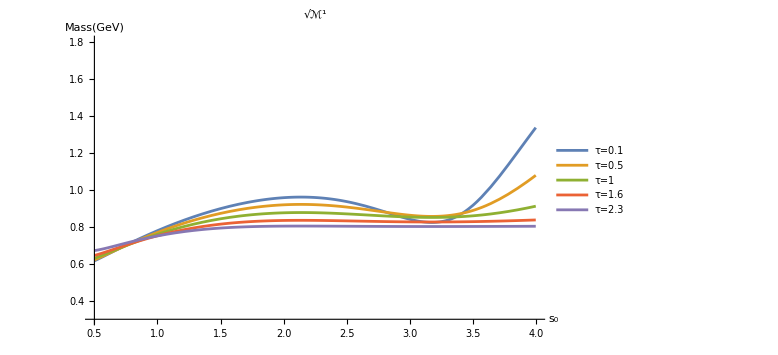

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

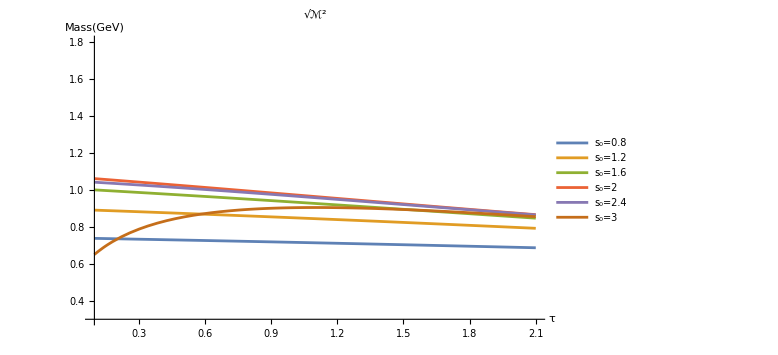
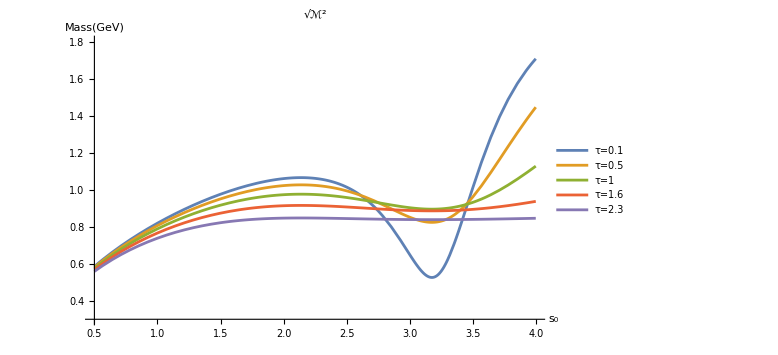

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

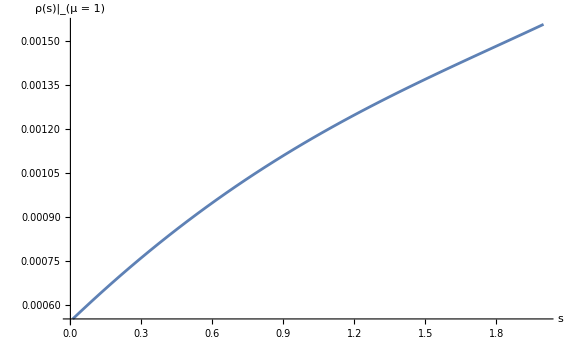
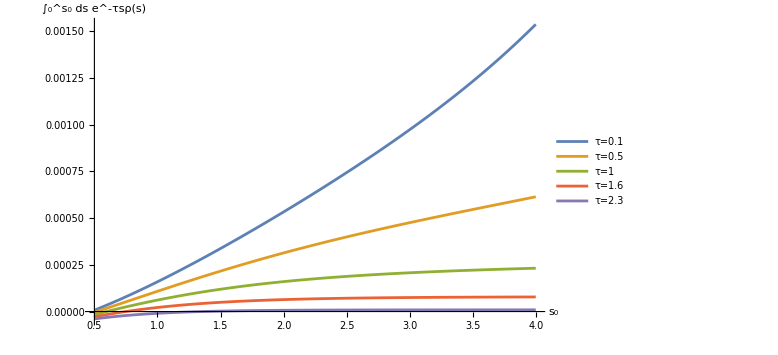

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

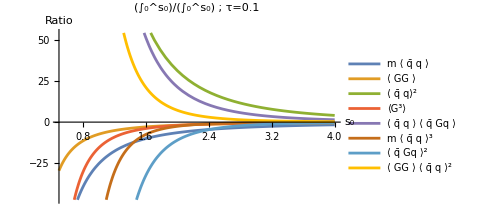
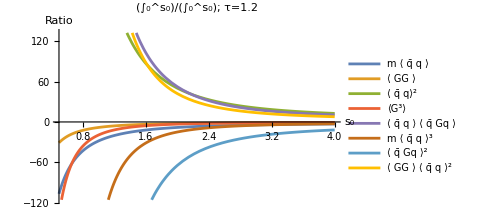
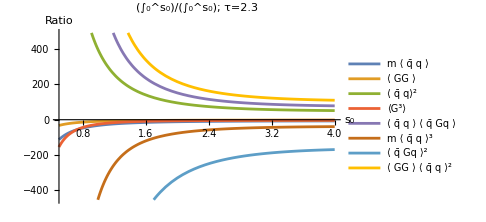

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

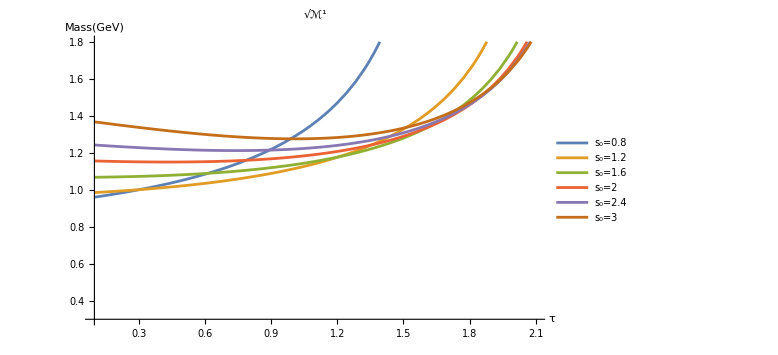
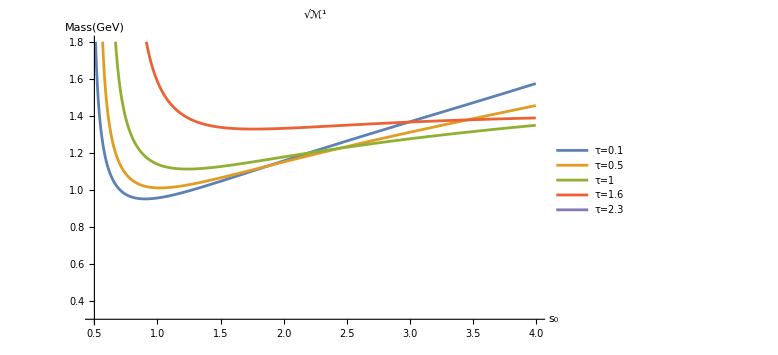

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5